```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,δ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ*c/k* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ*c/k* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -ρ*H[t]*R[t] -δ*H[t]- β*F[t],
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
```

```mathematica
N[RecurrenceTable[{B[n+1] == B[n]+1/7B[n],B[1]==1*10^(-7)},B,{n,1,75}]]
```

{1.×10^-7,1.14286×10^-7,1.30612×10^-7,1.49271×10^-7,1.70596×10^-7,1.94966×10^-7,2.22819×10^-7,2.5465×10^-7,2.91029×10^-7,3.32604×10^-7,3.80119×10^-7,4.34422×10^-7,4.96482×10^-7,5.67408×10^-7,6.48466×10^-7,7.41104×10^-7,8.46976×10^-7,9.67973×10^-7,1.10625×10^-6,1.26429×10^-6,1.4449×10^-6,1.65132×10^-6,1.88722×10^-6,2.15682×10^-6,2.46494×10^-6,2.81708×10^-6,3.21952×10^-6,3.67945×10^-6,4.20508×10^-6,4.80581×10^-6,5.49235×10^-6,6.27697×10^-6,7.17369×10^-6,8.1985×10^-6,9.36971×10^-6,0.0000107082,0.000012238,0.0000139863,0.0000159843,0.0000182678,0.0000208775,0.00002386,0.0000272685,0.000031164,0.000035616,0.000040704,0.0000465189,0.0000531645,0.0000607594,0.0000694393,0.0000793592,0.0000906962,0.000103653,0.00011846,0.000135383,0.000154724,0.000176827,0.000202088,0.000230958,0.000263952,0.000301659,0.000344754,0.000394004,0.00045029,0.000514618,0.000588134,0.000672154,0.000768175,0.000877915,0.00100333,0.00114666,0.00131047,0.00149768,0.00171164,0.00195616}

```mathematica
N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==1*10^(-8)},B,{n,1,43}]]
```

{1.×10^-8,1.25×10^-8,1.5625×10^-8,1.95313×10^-8,2.44141×10^-8,3.05176×10^-8,3.8147×10^-8,4.76837×10^-8,5.96046×10^-8,7.45058×10^-8,9.31323×10^-8,1.16415×10^-7,1.45519×10^-7,1.81899×10^-7,2.27374×10^-7,2.84217×10^-7,3.55271×10^-7,4.44089×10^-7,5.55112×10^-7,6.93889×10^-7,8.67362×10^-7,1.0842×10^-6,1.35525×10^-6,1.69407×10^-6,2.11758×10^-6,2.64698×10^-6,3.30872×10^-6,4.1359×10^-6,5.16988×10^-6,6.46235×10^-6,8.07794×10^-6,0.0000100974,0.0000126218,0.0000157772,0.0000197215,0.0000246519,0.0000308149,0.0000385186,0.0000481482,0.0000601853,0.0000752316,0.0000940395,0.000117549}

```mathematica
(*Don't go above 0.008457893893047288*)
```

```mathematica
Quiet[(
sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/7B[n],B[1]==1*10^(-7)},B,{n,1,75}]];
rhovalues =   sigvalues;
(*sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];
rhovalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];*)
Mass = 10^2;
threshold =(N[FSS+HSS]/.{α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality})*0.2/.M->Mass;
ExtinctionSigma =
ParallelTable[
(*Print[{sigma,rho}];*)
Reps = 50;
ProportionExtinct=
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=sigma,ρ=rho,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=-(α λ μ^2 (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-(α λ^2 μ (μ+2 ρ) (λ-σ))/((2 λ ρ+μ σ) (λ (2 δ λ+2 β μ-λ μ) ρ+μ (β μ+λ (δ+ρ)) σ))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=(μ (-λ+σ))/(2 λ ρ+μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
(*Rtraj = Flatten[Traj,1][[100;;1000,3]];*)
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
)]
```

NDSolve::nderr: Error test failure at t == 1.38576×10^8; unable to continue.

InterpolatingFunction::dmval: Input value {140000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 1.50538×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 1.57161×10^8; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.22601×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.92262×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.46452×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.89982×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9900000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.97692×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 4.12114×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 7.76068×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 8.95378×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 9.77678×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.92959×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8930000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 4.7997×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.47224×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.49299×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {6500000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.62212×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 5.69431×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.65907×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.72888×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.19306×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.76196×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.33714×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.58193×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.24592×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9250000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.72787×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.70269×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.91414×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9920000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.76039×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.48999×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.42046×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.96999×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.42511×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.65211×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8660000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.36805×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.52597×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.15083×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7160000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.41972×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.31568×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.29202×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.67794×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::singls: Encountered a singular linear system at t = 2.63144×10^9. Unable to continue.

NDSolve::nderr: Error test failure at t == 8.16551×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8170000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.98503×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.66748×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.97245×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8980000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.69551×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.52633×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 9.67383×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 5.75394×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {5760000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.24402×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.88911×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.40695×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 7.96121×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7970000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.51712×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.43219×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 9.48639×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 9.95428×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 9.70668×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.61699×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 6.03375×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 5.4511×10^9. Unable to continue.

NDSolve::ndsz: At t == 5.36996×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 9.12621×10^9. Unable to continue.

```mathematica
(*Save the Data*)
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_102.csv"}],ExtinctionSigma,"CSV"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_102.csv

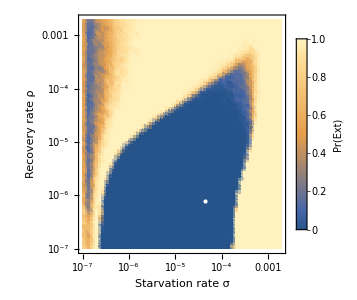

```mathematica
ExtPlot=Show[{
ListDensityPlot[MapAt[Log,Flatten[ExtinctionSigma,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[sigvalues]),Log@(Max[sigvalues])},{Log@(Min[sigvalues]),Log@(Max[sigvalues])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"Starvation rate σ","Recovery rate ρ"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}]}]
}]
```

```mathematica
{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}
```

{Log[-(6.71429×10^-6)/(M^(1/4) Log[1-0.0202 M^0.19])],Log[-(1.67857×10^-6)/(M^(1/4) Log[0.292893/(1-0.707107 (1-0.0202 M^0.19)^(1/4))])]}

```mathematica
Starvation
```

0.

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2.pdf"}],ExtPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2.pdf

```mathematica
threshold =(N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]/.{α->Resourcegrowth,λ->Growth,σ->Starvation,ρ->Recovery,β->Maintenance,μ->Mortality})*0.2/.M->Mass
```

16.6738

```mathematica
Mass
```

10

```mathematica
ts=Table[t,{t,0,100000000,100000}];
```

```mathematica
ts[[5]]
```

400000

```mathematica
ts[[1001]]
```

100000000

```mathematica
4*10^5
```

400000

```mathematica
sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==4*10^(-6)},B,{n,1,50}]]
```

{4.×10^-6,5.×10^-6,6.25×10^-6,7.8125×10^-6,9.76563×10^-6,0.000012207,0.0000152588,0.0000190735,0.0000238419,0.0000298023,0.0000372529,0.0000465661,0.0000582077,0.0000727596,0.0000909495,0.000113687,0.000142109,0.000177636,0.000222045,0.000277556,0.000346945,0.000433681,0.000542101,0.000677626,0.000847033,0.00105879,0.00132349,0.00165436,0.00206795,0.00258494,0.00323117,0.00403897,0.00504871,0.00631089,0.00788861,0.00986076,0.012326,0.0154074,0.0192593,0.0240741,0.0300927,0.0376158,0.0470198,0.0587747,0.0734684,0.0918355,0.114794,0.143493,0.179366,0.224208}

```mathematica
(*For M=10^3*)
```

```mathematica
N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==1*10^(-8)},B,{n,1,43}]]
```

{1.×10^-8,1.25×10^-8,1.5625×10^-8,1.95313×10^-8,2.44141×10^-8,3.05176×10^-8,3.8147×10^-8,4.76837×10^-8,5.96046×10^-8,7.45058×10^-8,9.31323×10^-8,1.16415×10^-7,1.45519×10^-7,1.81899×10^-7,2.27374×10^-7,2.84217×10^-7,3.55271×10^-7,4.44089×10^-7,5.55112×10^-7,6.93889×10^-7,8.67362×10^-7,1.0842×10^-6,1.35525×10^-6,1.69407×10^-6,2.11758×10^-6,2.64698×10^-6,3.30872×10^-6,4.1359×10^-6,5.16988×10^-6,6.46235×10^-6,8.07794×10^-6,0.0000100974,0.0000126218,0.0000157772,0.0000197215,0.0000246519,0.0000308149,0.0000385186,0.0000481482,0.0000601853,0.0000752316,0.0000940395,0.000117549}

```mathematica
N[RecurrenceTable[{B[n+1] == B[n]+1/7.5B[n],B[1]==1*10^(-8)},B,{n,1,75}]]
```

{1.×10^-8,1.13333×10^-8,1.28444×10^-8,1.4557×10^-8,1.6498×10^-8,1.86977×10^-8,2.11907×10^-8,2.40162×10^-8,2.72183×10^-8,3.08474×10^-8,3.49604×10^-8,3.96218×10^-8,4.49047×10^-8,5.0892×10^-8,5.76776×10^-8,6.5368×10^-8,7.40837×10^-8,8.39615×10^-8,9.51564×10^-8,1.07844×10^-7,1.22223×10^-7,1.38519×10^-7,1.56989×10^-7,1.77921×10^-7,2.01643×10^-7,2.28529×10^-7,2.59×10^-7,2.93533×10^-7,3.32671×10^-7,3.77027×10^-7,4.27297×10^-7,4.8427×10^-7,5.48839×10^-7,6.22018×10^-7,7.04954×10^-7,7.98947×10^-7,9.05474×10^-7,1.0262×10^-6,1.16303×10^-6,1.3181×10^-6,1.49385×10^-6,1.69303×10^-6,1.91877×10^-6,2.1746×10^-6,2.46455×10^-6,2.79315×10^-6,3.16557×10^-6,3.58765×10^-6,4.066×10^-6,4.60814×10^-6,5.22256×10^-6,5.9189×10^-6,6.70808×10^-6,7.60249×10^-6,8.61616×10^-6,9.76498×10^-6,0.000011067,0.0000125426,0.0000142149,0.0000161102,0.0000182583,0.0000206927,0.0000234517,0.0000265786,0.0000301225,0.0000341388,0.0000386906,0.0000438494,0.000049696,0.0000563221,0.0000638317,0.0000723426,0.0000819883,0.00009292,0.000105309}

```mathematica
Quiet[(
sigvalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/7.5B[n],B[1]==1*10^(-8)},B,{n,1,75}]];
rhovalues =   sigvalues;
(*sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];
rhovalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];*)
Mass = 10^3;
threshold =(N[FSS+HSS]/.{α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality})*0.2/.M->Mass;
ExtinctionSigma =
ParallelTable[
(*Print[{sigma,rho}];*)
Reps = 50;
ProportionExtinct=
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=sigma,ρ=rho,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=-((4535 α λ μ^2 (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-((4535 α λ^2 μ (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=-(4535 μ (λ-σ))/(9071 λ ρ+4535 μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
(*Rtraj = Flatten[Traj,1][[100;;1000,3]];*)
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
)]
```

NDSolve::ndsz: At t == 1.81563×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 1.13288×10^8; unable to continue.

NDSolve::ndsz: At t == 2.90724×10^8, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {20000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {120000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {120000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {120000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {300000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.95567×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 9.13451×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 3.21848×10^8; unable to continue.

NDSolve::ndsz: At t == 1.81404×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 9.05085×10^7; unable to continue.

NDSolve::ndsz: At t == 3.42646×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.29409×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 9.81644×10^7; unable to continue.

NDSolve::ndsz: At t == 5.13374×10^7, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.01711×10^7; unable to continue.

NDSolve::ndsz: At t == 5.49046×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 2.3249×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 9.44684×10^7; unable to continue.

NDSolve::ndsz: At t == 5.0582×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 2.98861×10^8; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.14288×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9150000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 8.81561×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 8.11768×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.32903×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 7.82029×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.39586×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 3.97093×10^9. Unable to continue.

NDSolve::nderr: Error test failure at t == 8.71996×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8720000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.31943×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 6.68401×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.62817×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.93803×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.79566×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 1.26621×10^9. Unable to continue.

NDSolve::nderr: Error test failure at t == 5.50999×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {5510000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.93422×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.48361×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 8.15314×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.28914×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.61712×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.67918×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7680000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.04727×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.38599×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.77838×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7780000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.70527×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.38249×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.98703×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.05926×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.72232×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 4.69054×10^9. Unable to continue.

NDSolve::singls: Encountered a singular linear system at t = 6.08478×10^9. Unable to continue.

NDSolve::nderr: Error test failure at t == 7.61421×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7620000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.15288×10^9; unable to continue.

NDSolve::singls: Encountered a singular linear system at t = 6.61976×10^9. Unable to continue.

NDSolve::nderr: Error test failure at t == 5.993×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.54114×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7550000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.83801×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 6.54873×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.11876×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9120000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.29673×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.20012×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_103.csv"}],ExtinctionSigma,"CSV"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_103.csv

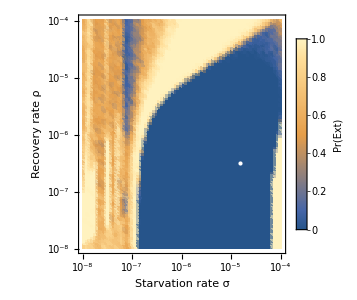

```mathematica
ExtPlot103=Show[{
ListDensityPlot[MapAt[Log,Flatten[ExtinctionSigma,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[sigvalues]),Log@(Max[sigvalues])},{Log@(Min[sigvalues]),Log@(Max[sigvalues])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"Starvation rate σ","Recovery rate ρ"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2_103.pdf"}],ExtPlot103,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2_103.pdf

```mathematica
(*For M=10^4*)
```

```mathematica
Quiet[(
sigvalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/7.5B[n],B[1]==1*10^(-8)},B,{n,1,75}]];
rhovalues =   sigvalues;
(*sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];
rhovalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];*)
Mass = 10^4;
threshold =(N[FSS+HSS]/.{α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality})*0.2/.M->Mass;
ExtinctionSigma =
ParallelTable[
(*Print[{sigma,rho}];*)
Reps = 50;
ProportionExtinct=
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=sigma,ρ=rho,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=-((4535 α λ μ^2 (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-((4535 α λ^2 μ (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=-(4535 μ (λ-σ))/(9071 λ ρ+4535 μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
(*Rtraj = Flatten[Traj,1][[100;;1000,3]];*)
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
)]
```

NDSolve::ndsz: At t == 1.93603×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 6.5726×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 1.80071×10^8; unable to continue.

InterpolatingFunction::dmval: Input value {20000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {70000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {190000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {70000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {190000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {20000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {70000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {190000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.11135×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 6.60662×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.83231×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.90111×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 8.77821×10^7; unable to continue.

NDSolve::ndsz: At t == 2.28844×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 6.31592×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.14518×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 8.99386×10^7; unable to continue.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.78595×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 9.66623×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 2.05369×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 9.63476×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 9.57921×10^7; unable to continue.

NDSolve::nderr: Error test failure at t == 2.54312×10^8; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.23218×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {6240000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.30305×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 5.27048×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.77513×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.5045×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.22699×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 5.8475×10^9. Unable to continue.

NDSolve::singls: Encountered a singular linear system at t = 8.33733×10^9. Unable to continue.

NDSolve::singls: Encountered a singular linear system at t = 2.33093×10^9. Unable to continue.

NDSolve::nderr: Error test failure at t == 6.99267×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.60737×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.24815×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.69811×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.37035×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.06732×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.62077×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9630000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.23988×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.38078×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.07237×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 8.54447×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.23511×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.24997×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {6250000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.32127×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.59869×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.47485×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.29801×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.2017×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.82583×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9830000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.72737×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 6.08961×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 5.91587×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {5920000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.45503×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 6.43896×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.81115×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7820000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.23684×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.85494×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.5565×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9560000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.82477×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.02488×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.86963×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9870000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.64311×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.88201×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_104.csv"}],ExtinctionSigma,"CSV"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_104.csv

```mathematica
(*For M=10^5*)
```

```mathematica
Quiet[(
sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/7.5B[n],B[1]==1*10^(-8)},B,{n,1,75}]];
rhovalues =   sigvalues;
(*sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];
rhovalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];*)
Mass = 10^5;
threshold =(N[FSS+HSS]/.{α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality})*0.2/.M->Mass;
ExtinctionSigma =
ParallelTable[
(*Print[{sigma,rho}];*)
Reps = 50;
ProportionExtinct=
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=sigma,ρ=rho,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=-((4535 α λ μ^2 (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-((4535 α λ^2 μ (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=-(4535 μ (λ-σ))/(9071 λ ρ+4535 μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
(*Rtraj = Flatten[Traj,1][[100;;1000,3]];*)
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
)]
```

NDSolve::ndsz: At t == 7.71085×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 7.31907×10^8, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {80000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {740000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {80000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {740000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {80000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {740000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 9.72748×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 7.96806×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 7.89103×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 7.54294×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 3.97009×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 3.38102×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 3.65357×10^8; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 4.24495×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 8.02749×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 4.14969×10^8; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.0952×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8100000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.363×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.48497×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.27559×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 8.37288×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.56843×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.98752×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {6990000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.18444×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.13803×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.5621×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.94995×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.49816×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::singls: Encountered a singular linear system at t = 3.55088×10^9. Unable to continue.

NDSolve::nderr: Error test failure at t == 4.91416×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {4920000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.52393×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.22334×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.76255×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.23389×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.14399×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.64023×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {6650000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.79726×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.51204×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.82794×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.40125×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.40934×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.58432×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9590000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.17923×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 6.81525×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.56085×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.76177×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.6414×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.08418×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7090000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.82148×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.81546×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.20795×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.75332×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.05259×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.0096×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8010000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.84153×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.69836×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.4487×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9450000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.06751×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.6472×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.87797×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9880000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.9021×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.42217×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.90982×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7910000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.9618×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.06453×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_105.csv"}],ExtinctionSigma,"CSV"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_105.csv

```mathematica
(*For M=10^6*)
```

```mathematica
N[RecurrenceTable[{B[n+1] == B[n]+1/2B[n],B[1]==1*10^(-8)},B,{n,1,25}]]
```

{1.×10^-8,1.5×10^-8,2.25×10^-8,3.375×10^-8,5.0625×10^-8,7.59375×10^-8,1.13906×10^-7,1.70859×10^-7,2.56289×10^-7,3.84434×10^-7,5.7665×10^-7,8.64976×10^-7,1.29746×10^-6,1.9462×10^-6,2.91929×10^-6,4.37894×10^-6,6.56841×10^-6,9.85261×10^-6,0.0000147789,0.0000221684,0.0000332526,0.0000498789,0.0000748183,0.000112227,0.000168341}

```mathematica
N[RecurrenceTable[{B[n+1] == B[n]+1/4B[n],B[1]==1*10^(-8)},B,{n,1,43}]]
```

{1.×10^-8,1.25×10^-8,1.5625×10^-8,1.95313×10^-8,2.44141×10^-8,3.05176×10^-8,3.8147×10^-8,4.76837×10^-8,5.96046×10^-8,7.45058×10^-8,9.31323×10^-8,1.16415×10^-7,1.45519×10^-7,1.81899×10^-7,2.27374×10^-7,2.84217×10^-7,3.55271×10^-7,4.44089×10^-7,5.55112×10^-7,6.93889×10^-7,8.67362×10^-7,1.0842×10^-6,1.35525×10^-6,1.69407×10^-6,2.11758×10^-6,2.64698×10^-6,3.30872×10^-6,4.1359×10^-6,5.16988×10^-6,6.46235×10^-6,8.07794×10^-6,0.0000100974,0.0000126218,0.0000157772,0.0000197215,0.0000246519,0.0000308149,0.0000385186,0.0000481482,0.0000601853,0.0000752316,0.0000940395,0.000117549}

```mathematica
N[RecurrenceTable[{B[n+1] == B[n]+1/6B[n],B[1]==1*10^(-8)},B,{n,1,61}]]
```

{1.×10^-8,1.16667×10^-8,1.36111×10^-8,1.58796×10^-8,1.85262×10^-8,2.16139×10^-8,2.52163×10^-8,2.9419×10^-8,3.43221×10^-8,4.00425×10^-8,4.67162×10^-8,5.45023×10^-8,6.3586×10^-8,7.41837×10^-8,8.65476×10^-8,1.00972×10^-7,1.17801×10^-7,1.37434×10^-7,1.6034×10^-7,1.87063×10^-7,2.18241×10^-7,2.54614×10^-7,2.9705×10^-7,3.46558×10^-7,4.04318×10^-7,4.71704×10^-7,5.50322×10^-7,6.42042×10^-7,7.49049×10^-7,8.7389×10^-7,1.01954×10^-6,1.18946×10^-6,1.38771×10^-6,1.61899×10^-6,1.88882×10^-6,2.20362×10^-6,2.5709×10^-6,2.99938×10^-6,3.49927×10^-6,4.08249×10^-6,4.7629×10^-6,5.55672×10^-6,6.48284×10^-6,7.56331×10^-6,8.82386×10^-6,0.0000102945,0.0000120103,0.000014012,0.0000163473,0.0000190718,0.0000222505,0.0000259589,0.0000302854,0.0000353329,0.0000412218,0.0000480921,0.0000561074,0.0000654586,0.0000763684,0.0000890965,0.000103946}

```mathematica
Quiet[(
sigvalues =   N[RecurrenceTable[{B[n+1] == B[n]+1/7.5B[n],B[1]==1*10^(-8)},B,{n,1,75}]];
rhovalues =   sigvalues;
(*sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];
rhovalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];*)
Mass = 10^6;
threshold =(N[FSS+HSS]/.{α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality})*0.2/.M->Mass;
ExtinctionSigma =
ParallelTable[
(*Print[{sigma,rho}];*)
Reps = 25;
ProportionExtinct=
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=sigma,ρ=rho,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=-((4535 α λ μ^2 (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-((4535 α λ^2 μ (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=-(4535 μ (λ-σ))/(9071 λ ρ+4535 μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
(*Rtraj = Flatten[Traj,1][[100;;1000,3]];*)
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
)]
```

NDSolve::ndsz: At t == 3.91233×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 2.09285×10^8; unable to continue.

NDSolve::ndsz: At t == 1.17686×10^9, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {40000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {210000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1180000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {40000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {210000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1180000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {40000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {210000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1180000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 6.21432×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 2.57621×10^8; unable to continue.

NDSolve::ndsz: At t == 5.94925×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.00659×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.25102×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 9.7822×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 1.98778×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 1.62529×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 2.18261×10^8; unable to continue.

NDSolve::nderr: Error test failure at t == 1.74846×10^8; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 1.77735×10^8; unable to continue.

NDSolve::ndsz: At t == 1.16223×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.26244×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.41267×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.53478×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 5.88691×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {5890000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.04238×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.84836×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.78745×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.62721×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.77717×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.13305×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8140000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.78836×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.52888×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.61059×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.26071×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.87093×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 5.6558×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {5660000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 6.7932×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.1217×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.67736×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.30152×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.1715×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.37026×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {7380000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.01093×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.44685×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.38638×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.78615×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.62722×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.35523×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9360000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.90067×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.33821×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.61027×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.43804×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.06131×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.99364×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.45728×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.23157×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.96562×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9970000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 7.97702×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 7.97472×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.38224×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9390000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.24699×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.59449×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_106.csv"}],ExtinctionSigma]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_106.csv

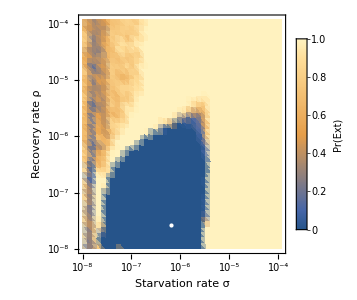

```mathematica
ExtPlot106=Show[{
ListDensityPlot[MapAt[Log,Flatten[ExtinctionSigma,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[sigvalues]),Log@(Max[sigvalues])},{Log@(Min[sigvalues]),Log@(Max[sigvalues])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"Starvation rate σ","Recovery rate ρ"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->Mass),Log@(Recovery/.M->Mass)}]}]
}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2_106.pdf"}],ExtPlot106,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometric2_106.pdf

```mathematica
(*For M=10^7*)
```

```mathematica
Quiet[(
sigvalues =   N[RecurrenceTable[{B[n+1] == B[n]+1/7.5B[n],B[1]==1*10^(-8)},B,{n,1,75}]];
rhovalues =   sigvalues;
(*sigvalues = N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];
rhovalues =  N[RecurrenceTable[{B[n+1] == B[n]+1/3B[n],B[1]==4*10^(-8)},B,{n,1,48}]];*)
Mass = 10^7;
threshold =(N[FSS+HSS]/.{α->ResourceGrowth,λ->ConsumerGrowth,σ->Starvation,ρ->Recovery,β->FullMaintenance,δ->StarveMaintenance,μ->Mortality})*0.2/.M->Mass;
ExtinctionSigma =
ParallelTable[
(*Print[{sigma,rho}];*)
Reps = 50;
ProportionExtinct=
With[{
α=ResourceGrowth,λ=ConsumerGrowth,σ=sigma,ρ=rho,β=FullMaintenance,δ=StarveMaintenance,μ=Mortality,T=10000000000,PercentPerturbed=1},
M=Mass;
ExtinctionReps = Table[
F0=-((4535 α λ μ^2 (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
H0=-((4535 α λ^2 μ (4535 μ+9071 ρ) (λ-σ))/((9071 λ ρ+4535 μ σ) (λ (9071 δ λ+9071 β μ-4535 λ μ) ρ+4535 μ (β μ+λ (δ+ρ)) σ)))*(1+RandomReal[{-PercentPerturbed,PercentPerturbed}]);
R0=-(4535 μ (λ-σ))/(9071 λ ρ+4535 μ σ);
(*Set threshold as percent of equilibrial state*)
(*threshold =16.673810837201515;*)(*N[(α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))+(α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ))]*0.4;*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,δ,T,F0,H0,R0]],{t,0,T,T/1000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
(*Rtraj = Flatten[Traj,1][[100;;1000,3]];*)
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma,rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigvalues},{rho,rhovalues}];
)]
```

NDSolve::ndsz: At t == 3.04035×10^8, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {310000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 1.00999×10^9; unable to continue.

NDSolve::ndsz: At t == 2.15475×10^8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 6.55476×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 9.56549×10^8; unable to continue.

InterpolatingFunction::dmval: Input value {6560000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::nderr: Error test failure at t == 9.7174×10^8; unable to continue.

InterpolatingFunction::dmval: Input value {6560000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {6560000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At t == 3.91703×10^8, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 3.70072×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 9.15784×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 6.99647×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 4.60003×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.36434×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.17459×10^9, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {4180000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.67068×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::nderr: Error test failure at t == 8.46265×10^9; unable to continue.

NDSolve::ndsz: At t == 5.92968×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.47495×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.4053×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.5625×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8570000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.88087×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.79784×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 2.20272×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.74667×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 1.63479×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.83698×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9840000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.20371×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.89809×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 4.40124×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.13568×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 6.3971×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.90479×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9910000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.50968×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.3854×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.98192×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.22554×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.29812×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.96045×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9970000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.51385×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.69306×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.63598×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9640000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.99582×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.86862×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 6.87024×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.36198×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 6.55618×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 5.00121×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.334×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.15404×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.77795×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9780000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.46204×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.95931×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::ndsz: At t == 7.10051×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 3.64786×10^9, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 7.43517×10^9, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.92872×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {9930000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.61926×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 8.68369×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 8.55026×10^9; unable to continue.

InterpolatingFunction::dmval: Input value {8560000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::nderr: Error test failure at t == 9.65998×10^9; unable to continue.

NDSolve::nderr: Error test failure at t == 9.3066×10^9; unable to continue.

General::stop: Further output of NDSolve::nderr will be suppressed during this calculation.

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_107.csv"}],ExtinctionSigma,"CSV"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_107.csv

```mathematica
(*Combined Figure*)
ES102 = ToExpression[Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_102.csv"}],"CSV"]
];
ES103 = ToExpression[Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_103.csv"}],"CSV"]
];
ES104= ToExpression[Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_104.csv"}],"CSV"]
];
ES105 = ToExpression[Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_105.csv"}],"CSV"]
];
ES106 = ToExpression[Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_106.csv"}],"CSV"]
];
ES107 = ToExpression[Import[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/NewRateFigures_Final/ExtData_107.csv"}],"CSV"]
];
```

```mathematica
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES102,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES102[[All,1,1]]]),Log@(Max[ES102[[All,1,1]]])},{Log@(Min[ES102[[All,1,1]]]),Log@(Max[ES102[[All,1,1]]])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"Starvation rate σ","Recovery rate ρ"},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^2),Log@(Recovery/.M->10^2)}]}]
}]
```

-Graphics-

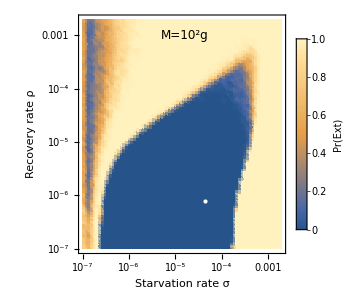
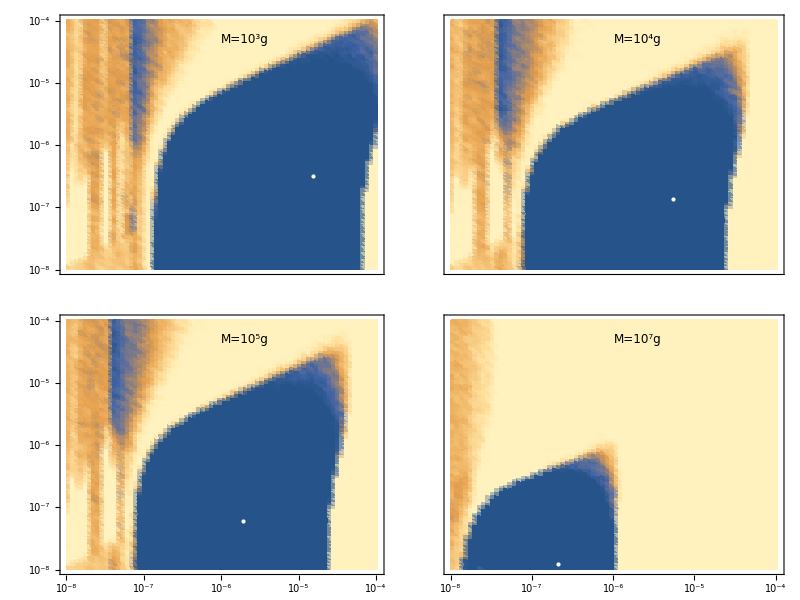
-Graphics- | -Graphics-

```mathematica
CombinedPlot=Legended[
Grid[{{
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES102,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES102[[All,1,1]]]),Log@(Max[ES102[[All,1,1]]])},{Log@(Min[ES102[[All,1,1]]]),Log@(Max[ES102[[All,1,1]]])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{Style["Starvation rate σ",FontSize->14],Style["Recovery rate ρ",FontSize->14]},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}}],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^2),Log@(Recovery/.M->10^2)}]}],
Graphics[Text[Style["M=10^2g",FontSize->12],{Log@(1*10^-4.8),Log@(1*10^-3)}]]
},ImageSize->300],
Grid[{{
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES103,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])},{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{Style["",FontSize->14],""},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{None,None}}],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^3),Log@(Recovery/.M->10^3)}]}],
Graphics[Text[Style["M=10^3g",FontSize->12],{Log@(1*10^-5.7),Log@(1*10^-4.3)}]]
},ImageSize->190],
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES104,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])},{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"",""},ImageSize->300,FrameTicks->{{None,None},{None,None}}],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^4),Log@(Recovery/.M->10^4)}]}],
Graphics[Text[Style["M=10^4g",FontSize->12],{Log@(1*10^-5.7),Log@(1*10^-4.3)}]]
},ImageSize->151]},{
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES105,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])},{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{Style["",FontSize->14],""},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}}],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^5),Log@(Recovery/.M->10^5)}]}],
Graphics[Text[Style["M=10^5g",FontSize->12],{Log@(1*10^-5.7),Log@(1*10^-4.3)}]]
},ImageSize->190],
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES107,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])},{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"",""},ImageSize->300,FrameTicks->{{None,None},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}}],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^7),Log@(Recovery/.M->10^7)}]}],
Graphics[Text[Style["M=10^7g",FontSize->12],{Log@(1*10^-5.7),Log@(1*10^-4.3)}]]
},ImageSize->151]
}},Spacings->{-0.5,-0.5}]
(*Show[{
ListDensityPlot[MapAt[Log,Flatten[ES106,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES106[[All,1,1]]]),Log@(Max[ES106[[All,1,1]]])},{Log@(Min[ES106[[All,1,1]]]),Log@(Max[ES106[[All,1,1]]])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"",""},ImageSize->300,FrameTicks->{{None,None},{Charting`ScaledTicks[{Log,Exp}],None}}(*,PlotLegends->BarLegend[True,LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]*)],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^6),Log@(Recovery/.M->10^6)}]}]
},ImageSize->250]*)
}}(*,ImageSize->1200*)],
BarLegend[{ColorData["M10DefaultDensityGradient"],{0,1}},(*Table[i,{i,0,1,1/10}],*)LegendMarkerSize->200,LegendLabel->"Pr(Ext)"]]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometricComb2.pdf"}],CombinedPlot,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometricComb2.pdf

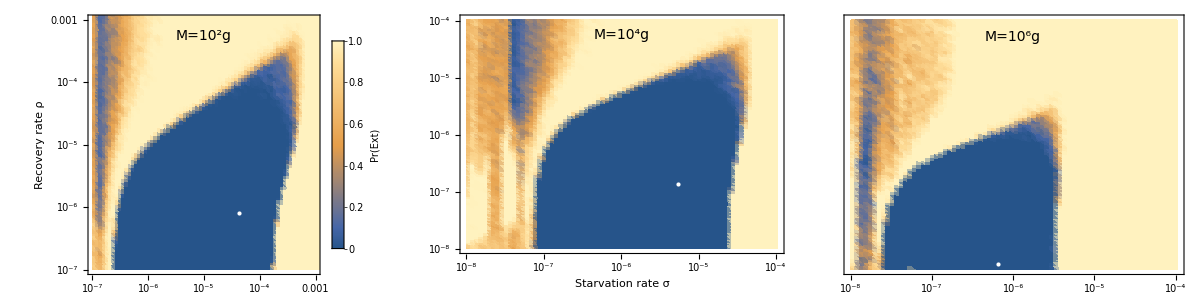

```mathematica
CombinedPlotRow=Legended[
Grid[{{
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES102,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES102[[All,1,1]]]),Log@(10^-3)},{Log@(Min[ES102[[All,1,1]]]),Log@(10^-3)}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{Style["",FontSize->14],Style["Recovery rate ρ",FontSize->14]},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}}],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^2),Log@(Recovery/.M->10^2)}]}],
Graphics[Text[Style["M=10^2g",FontSize->14],{Log@(1*10^-5),Log@(1*10^-3.25)}]]
},ImageSize->300],
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES104,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])},{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{Style["Starvation rate σ",FontSize->14],""},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],None},{Charting`ScaledTicks[{Log,Exp}],None}}],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^4),Log@(Recovery/.M->10^4)}]}],
Graphics[Text[Style["M=10^4g",FontSize->14],{Log@(1*10^-6),Log@(1*10^-4.25)}]]
},ImageSize->300],
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES106,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])},{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{"",""},ImageSize->300,FrameTicks->{{None,None},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}}],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^6),Log@(Recovery/.M->10^7)}]}],
Graphics[Text[Style["M=10^6g",FontSize->14],{Log@(1*10^-6),Log@(1*10^-4.25)}]]
},ImageSize->280]
}}(*,ImageSize->1200*),Spacings->{-0.5}],
BarLegend[{ColorData["M10DefaultDensityGradient"],{0,1}},(*Table[i,{i,0,1,1/10}],*)LegendMarkerSize->250,LegendLabel->"Pr(Ext)"]]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometricComb3.pdf"}],CombinedPlotRow,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_ExtinctionAllometricComb3.pdf

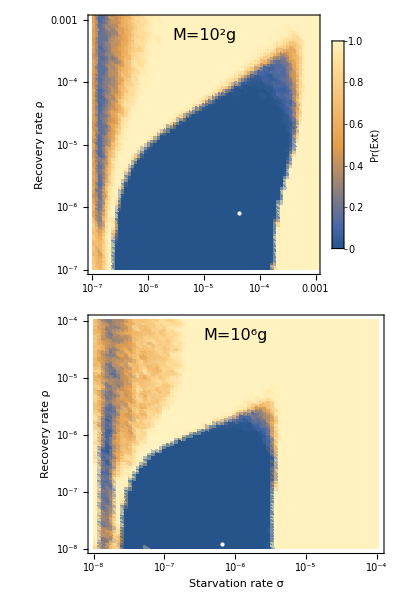

```mathematica
CombinedPlotRow2=Legended[
Grid[{{
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES102,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES102[[All,1,1]]]),Log@(10^-3)},{Log@(Min[ES102[[All,1,1]]]),Log@(10^-3)}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{Style["",FontSize->16],Style["Recovery rate ρ",FontSize->16]},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},FrameTicksStyle->Directive[16]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^2),Log@(Recovery/.M->10^2)}]}],
Graphics[Text[Style["M=10^2g",FontSize->16],{Log@(1*10^-5),Log@(1*10^-3.25)}]]
},ImageSize->310]},{
Show[{
ListDensityPlot[MapAt[Log,Flatten[ES106,1],{All, ;;2}],Mesh->None,PlotRange->{{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])},{Log@(Min[ES103[[All,1,1]]]),Log@(Max[ES103[[All,1,1]]])}},InterpolationOrder->3,(*ColorFunction->ColorData["DarkRainbow"],*)PlotRange->{-1,1},FrameLabel->{Style["Starvation rate σ",FontSize->16],Style["Recovery rate ρ",FontSize->16]},ImageSize->300,FrameTicks->{{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]},{Charting`ScaledTicks[{Log,Exp}],Charting`ScaledFrameTicks[{Log,Exp}]}},FrameTicksStyle->Directive[16]],
Graphics[{PointSize[Large],White,Point[{Log@(Starvation/.M->10^6),Log@(Recovery/.M->10^7)}]}],
Graphics[Text[Style["M=10^6g",FontSize->16],{Log@(1*10^-6),Log@(1*10^-4.25)}]]
},ImageSize->310]
}}(*,ImageSize->1200*),Spacings->{-0.5}],
BarLegend[{ColorData["M10DefaultDensityGradient"],{0,1}},(*Table[i,{i,0,1,1/10}],*)LegendMarkerSize->300,LegendLabel->"Pr(Ext)",LabelStyle->Directive[FontSize->16]]]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/NatureComm_REVISION/fig_ExtinctionAllometricComb4.pdf"}],CombinedPlotRow2,"PDF"]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/NatureComm_REVISION/fig_ExtinctionAllometricComb4.pdf